```mathematica
h=Flatten[Table[x^n  ,{n,0,5}]]
```

{1,x,x^2,x^3,x^4,x^5}

```mathematica
M=Flatten[Table[{a},{a,0,2}],1];M//MatrixForm
```

(0
1
2)

```mathematica
A[i_]:=D[#,{x,M[[i]]}]&
```

```mathematica
Co=Inverse[Transpose[Flatten[Table[A[j][h]/.x->M[[i]],{j,3},{i,2}],1]]];
```

```mathematica
sc[m_ ]:=DiagonalMatrix [  {1,1,m,m,m^2,m^2}];
```

```mathematica
alexp=sc[b].Co.h/.x->y/b
```

{1-(10 y^3)/b^3+(15 y^4)/b^4-(6 y^5)/b^5,(10 y^3)/b^3-(15 y^4)/b^4+(6 y^5)/b^5,y-(6 y^3)/b^2+(8 y^4)/b^3-(3 y^5)/b^4,-(4 y^3)/b^2+(7 y^4)/b^3-(3 y^5)/b^4,y^2/2-(3 y^3)/(2 b)+(3 y^4)/(2 b^2)-y^5/(2 b^3),y^3/(2 b)-y^4/b^2+y^5/(2 b^3)}

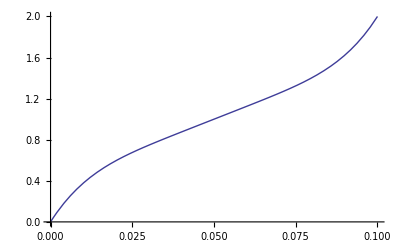

```mathematica
b=0.1;s={0,2,50,50,-3000,3000};Plot[s.alexp,{y,0,b}]
b=.
```

```mathematica
(*Probe:*)
Table[Table[D[{y1,y2,m1,m2,k1,k2}.alexp,{y,i}],{i,0,2}]/.y->j b,{j,0,1}]
```

{{y1,m1,k1},{y2,m2,k2}}